```mathematica
Table[ChromaticPolynomial[ReadGrof[k],x],{k,100,200,10}]
```

{-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,-8046 x+28071 x^2-41898 x^3+35643 x^4-19263 x^5+6921 x^6-1665 x^7+260 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,-7164 x+25476 x^2-38815 x^3+33692 x^4-18543 x^5+6764 x^6-1646 x^7+259 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10}

```mathematica
Table[DiscretePlot[LaplaceTransform[ChromaticPolynomial[ReadGrof[k],x],x,t],{t,-10,10}],{k,100,200,10}]
```

NIntegrate::inumri: The integrand ⅇ^(9.99959 x) (-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.23043×10^7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
Table[Assuming[{0<x<1},BernsteinBasis[k,1,x]//PiecewiseExpand],{k,1,10}]
```

{x,-2 (-1+x) x,3 (-1+x)^2 x,-4 (-1+x)^3 x,5 (-1+x)^4 x,-6 (-1+x)^5 x,7 (-1+x)^6 x,-8 (-1+x)^7 x,9 (-1+x)^8 x,-10 (-1+x)^9 x}

```mathematica
Clear[BoegaPoly];BoegaPoly[n_]:=BoegaPoly[n]=If[n==0,1,Assuming[{0<x<1},BernsteinBasis[k,1,x]//PiecewiseExpand]]
```

```mathematica
Table[BoegaPoly[k],{k,0,10}]
```

{1,x,-2 (-1+x) x,3 (-1+x)^2 x,-4 (-1+x)^3 x,5 (-1+x)^4 x,-6 (-1+x)^5 x,7 (-1+x)^6 x,-8 (-1+x)^7 x,9 (-1+x)^8 x,-10 (-1+x)^9 x}

```mathematica
BoegaBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = BoegaPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
BoegaBaseCoeff[-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10]
```

{0,0,-104,-288,-386,-312,-327/2,-396/7,-101/8,-5/3,-1/10}

```mathematica
Table[-BoegaBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]]*120*7,{k,100,200,10}]//TableForm
```

0 | 0 | 87360 | 241920 | 324240 | 262080 | 137340 | 47520 | 10605 | 1400 | 84
0 | 0 | 87360 | 241920 | 324240 | 262080 | 137340 | 47520 | 10605 | 1400 | 84
0 | 0 | 169680 | 416640 | 491610 | 350616 | 164220 | 51960 | 10920 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84
0 | 0 | 87360 | 241920 | 324240 | 262080 | 137340 | 47520 | 10605 | 1400 | 84
0 | 0 | 136080 | 348320 | 429450 | 319536 | 155260 | 50520 | 10815 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84
0 | 0 | 53760 | 161280 | 235200 | 206976 | 117600 | 43680 | 10290 | 1400 | 84

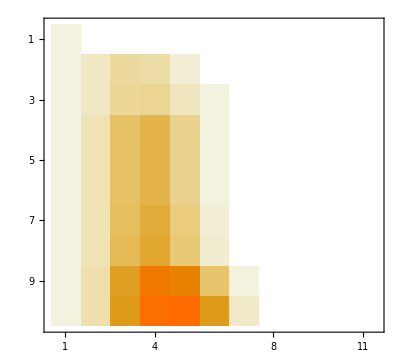

```mathematica
Table[Reverse[CompleteBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]]],{k,1,100,10}]//Sort//MatrixPlot
```

```mathematica
Table[PiecewiseExpand@BernsteinBasis[3,k,x],{k,0,3}]
```

{Piecewise[{{1, x==0}, {-(-1+x)^3, 0<x<1}, {0, True}}],Piecewise[{{3 (-1+x)^2 x, 0<x<1}, {0, True}}],Piecewise[{{-3 (-1+x) x^2, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^3, 0<x<1}, {0, True}}]}

```mathematica
InverseHankelTransform[-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,x,t]
```

(9 (2381400-1968575 t^2+427900 t^4-33183 t^6+630 t^8))/t^11

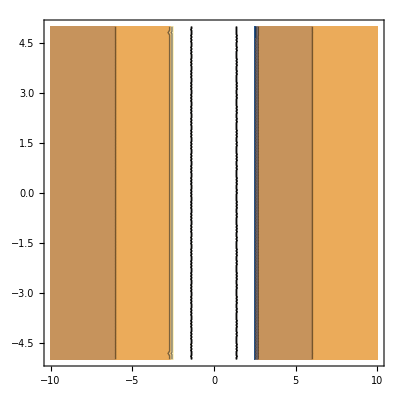

```mathematica
ContourPlot[(9 (2381400-1968575 t^2+427900 t^4-33183 t^6+630 t^8))/t^11,{t,-10,10},{y,-5,5}]
```

```mathematica
ChromaticPolynomial[ReadGrof[100],4]
```

120

```mathematica
InverseLaplaceTransform[ChromaticPolynomial[ReadGrof[100],x],x,t]
```

-5670 DiracDelta'[t]+20925 DiracDelta''[t]-33183 DiracDelta^(3)[t]+29973 DiracDelta^(4)[t]-17116 DiracDelta^(5)[t]+6444 DiracDelta^(6)[t]-1607 DiracDelta^(7)[t]+257 DiracDelta^(8)[t]-24 DiracDelta^(9)[t]+DiracDelta^(10)[t]

```mathematica
Simplify[%643]
```

-5670 DiracDelta'[t]+20925 DiracDelta''[t]-33183 DiracDelta^(3)[t]+29973 DiracDelta^(4)[t]-17116 DiracDelta^(5)[t]+6444 DiracDelta^(6)[t]-1607 DiracDelta^(7)[t]+257 DiracDelta^(8)[t]-24 DiracDelta^(9)[t]+DiracDelta^(10)[t]

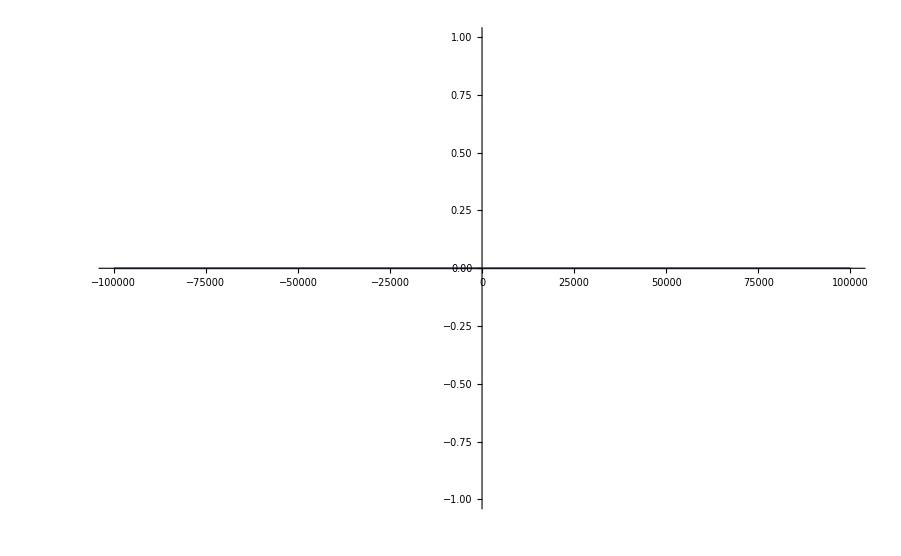

```mathematica
Plot[-5670 DiracDelta'[t]+20925 DiracDelta''[t]-33183 Derivative[3][DiracDelta][t]+29973 Derivative[4][DiracDelta][t]-17116 Derivative[5][DiracDelta][t]+6444 Derivative[6][DiracDelta][t]-1607 Derivative[7][DiracDelta][t]+257 Derivative[8][DiracDelta][t]-24 Derivative[9][DiracDelta][t]+Derivative[10][DiracDelta][t],{t,-100000,100000}]
```

```mathematica
ResourceFunction["CriticalPoints"][%643,t]
```

<||>

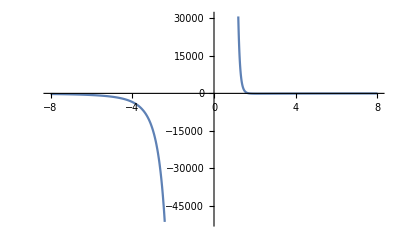

```mathematica
Plot[3628800/t^11-8709120/t^10+10362240/t^9-8099280/t^8+4639680/t^7-2053920/t^6+719352/t^5-199098/t^4+41850/t^3-5670/t^2,{t,-8,8}]
```

```mathematica
∫(3628800/t^11-8709120/t^10+10362240/t^9-8099280/t^8+4639680/t^7-2053920/t^6+719352/t^5-199098/t^4+41850/t^3-5670/t^2)ⅆt
```

-6 (60480/t^10-161280/t^9+215880/t^8-192840/t^7+128880/t^6-68464/t^5+29973/t^4-11061/t^3+6975/(2 t^2)-945/t)

```mathematica
∫-6 (60480/t^10-161280/t^9+215880/t^8-192840/t^7+128880/t^6-68464/t^5+29973/t^4-11061/t^3+6975/(2 t^2)-945/t)ⅆt
```

3 (13440/t^9-40320/t^8+61680/t^7-64280/t^6+51552/t^5-34232/t^4+19982/t^3-11061/t^2+6975/t+1890 Log[t])

```mathematica
∫3 (13440/t^9-40320/t^8+61680/t^7-64280/t^6+51552/t^5-34232/t^4+19982/t^3-11061/t^2+6975/t+1890 Log[t])ⅆt
```

-5040/t^8+17280/t^7-30840/t^6+38568/t^5-38664/t^4+34232/t^3-29973/t^2+33183/t-5670 t+20925 Log[t]+5670 t Log[t]

```mathematica
∫(-5040/t^8+17280/t^7-30840/t^6+38568/t^5-38664/t^4+34232/t^3-29973/t^2+33183/t-5670 t+20925 Log[t]+5670 t Log[t])ⅆt
```

720/t^7-2880/t^6+6168/t^5-9642/t^4+12888/t^3-17116/t^2+29973/t-20925 t-(8505 t^2)/2+33183 Log[t]+20925 t Log[t]+2835 t^2 Log[t]

```mathematica
∫(720/t^7-2880/t^6+6168/t^5-9642/t^4+12888/t^3-17116/t^2+29973/t-20925 t-(8505 t^2)/2+33183 Log[t]+20925 t Log[t]+2835 t^2 Log[t])ⅆt
```

-120/t^6+576/t^5-1542/t^4+3214/t^3-6444/t^2+17116/t-33183 t-(62775 t^2)/4-(3465 t^3)/2+29973 Log[t]+33183 t Log[t]+20925/2 t^2 Log[t]+945 t^3 Log[t]

```mathematica
∫(-120/t^6+576/t^5-1542/t^4+3214/t^3-6444/t^2+17116/t-33183 t-(62775 t^2)/4-(3465 t^3)/2+29973 Log[t]+33183 t Log[t]+20925/2 t^2 Log[t]+945 t^3 Log[t])ⅆt
```

24/t^5-144/t^4+514/t^3-1607/t^2+6444/t-29973 t-(99549 t^2)/4-(25575 t^3)/4-(7875 t^4)/16+17116 Log[t]+29973 t Log[t]+33183/2 t^2 Log[t]+6975/2 t^3 Log[t]+945/4 t^4 Log[t]

```mathematica
∫(24/t^5-144/t^4+514/t^3-1607/t^2+6444/t-29973 t-(99549 t^2)/4-(25575 t^3)/4-(7875 t^4)/16+17116 Log[t]+29973 t Log[t]+33183/2 t^2 Log[t]+6975/2 t^3 Log[t]+945/4 t^4 Log[t])ⅆt
```

-6/t^4+48/t^3-257/t^2+1607/t-17116 t-(89919 t^2)/4-(40557 t^3)/4-(58125 t^4)/32-(8631 t^5)/80+6444 Log[t]+17116 t Log[t]+29973/2 t^2 Log[t]+11061/2 t^3 Log[t]+6975/8 t^4 Log[t]+189/4 t^5 Log[t]

```mathematica
∫(-6/t^4+48/t^3-257/t^2+1607/t-17116 t-(89919 t^2)/4-(40557 t^3)/4-(58125 t^4)/32-(8631 t^5)/80+6444 Log[t]+17116 t Log[t]+29973/2 t^2 Log[t]+11061/2 t^3 Log[t]+6975/8 t^4 Log[t]+189/4 t^5 Log[t])ⅆt
```

2/t^3-24/t^2+257/t-6444 t-12837 t^2-(109901 t^3)/12-(92175 t^4)/32-(12741 t^5)/32-(3087 t^6)/160+1607 Log[t]+6444 t Log[t]+8558 t^2 Log[t]+9991/2 t^3 Log[t]+11061/8 t^4 Log[t]+1395/8 t^5 Log[t]+63/8 t^6 Log[t]

```mathematica
∫%635ⅆt
```

-1/t^2+24/t-1607 t-4833 t^2-(47069 t^3)/9-(249775 t^4)/96-(505119 t^5)/800-(4557 t^6)/64-(3267 t^7)/1120+257 Log[t]+1607 t Log[t]+3222 t^2 Log[t]+8558/3 t^3 Log[t]+9991/8 t^4 Log[t]+11061/40 t^5 Log[t]+465/16 t^6 Log[t]+9/8 t^7 Log[t]

```mathematica
∫%636ⅆt
```

1/t-257 t-(4821 t^2)/4-1969 t^3-(106975 t^4)/72-(1368767 t^5)/2400-(180663 t^6)/1600-(33759 t^7)/3136-(6849 t^8)/17920+24 Log[t]+257 t Log[t]+1607/2 t^2 Log[t]+1074 t^3 Log[t]+4279/6 t^4 Log[t]+9991/40 t^5 Log[t]+3687/80 t^6 Log[t]+465/112 t^7 Log[t]+9/64 t^8 Log[t]

```mathematica
∫%637ⅆt
```

-24 t-(771 t^2)/4-(17677 t^3)/36-(4475 t^4)/8-(586223 t^5)/1800-(489559 t^6)/4800-(1338381 t^7)/78400-(70773 t^8)/50176-(7129 t^9)/161280+Log[t]+24 t Log[t]+257/2 t^2 Log[t]+1607/6 t^3 Log[t]+537/2 t^4 Log[t]+4279/30 t^5 Log[t]+9991/240 t^6 Log[t]+3687/560 t^7 Log[t]+465/896 t^8 Log[t]+1/64 t^9 Log[t]

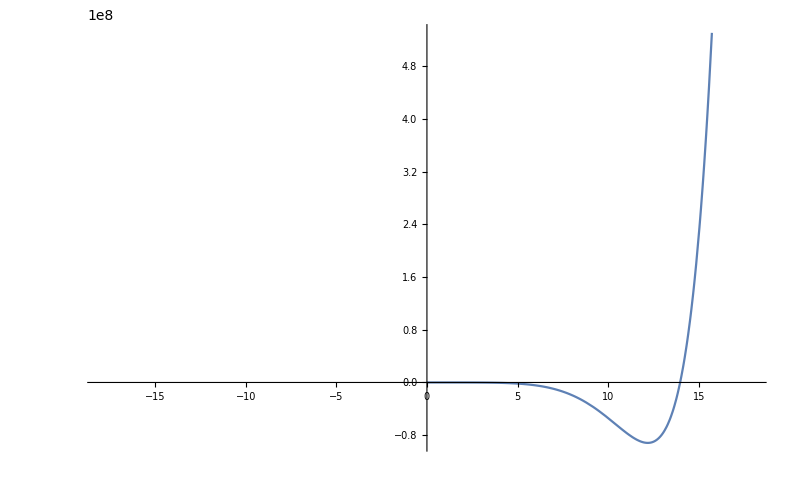

```mathematica
Plot[%638,{t,-18.,18.}]
```